```mathematica
SetOptions[$FrontEnd,"DynamicUpdating"->False]
```

NDSolve::precw: The precision of the differential equation ({{{{-25000000-1.40989×10^13 Cos[«1»] Power[«2»] Power[«2»] Sin[«1»]-1.40989×10^13 Cos[«1»] Power[«2»] Power[«2»] Sin[«1»]-5.×10^12 Sin[«1»] («1»)^(«1»)[«1»] Plus[«2»]+5000000000000 Power[«2»] («1»)^(«1»)[«1»]}}==0,{{«4»+5000000000000 (««1»«1»)^(«1»)[«1»]}}==0,α[0]==π/6,α'[0]==0,ψ[0]==0,ψ'[0]==0},{},{},{},{}}) is less than WorkingPrecision (10.).

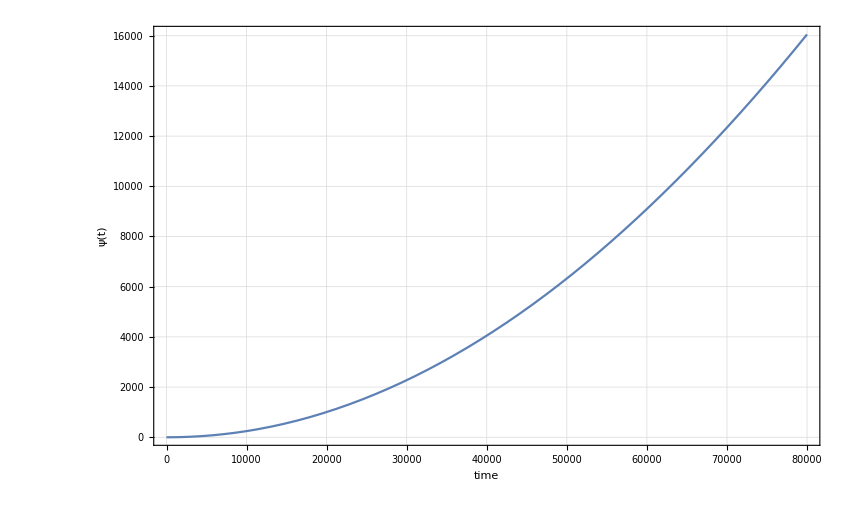

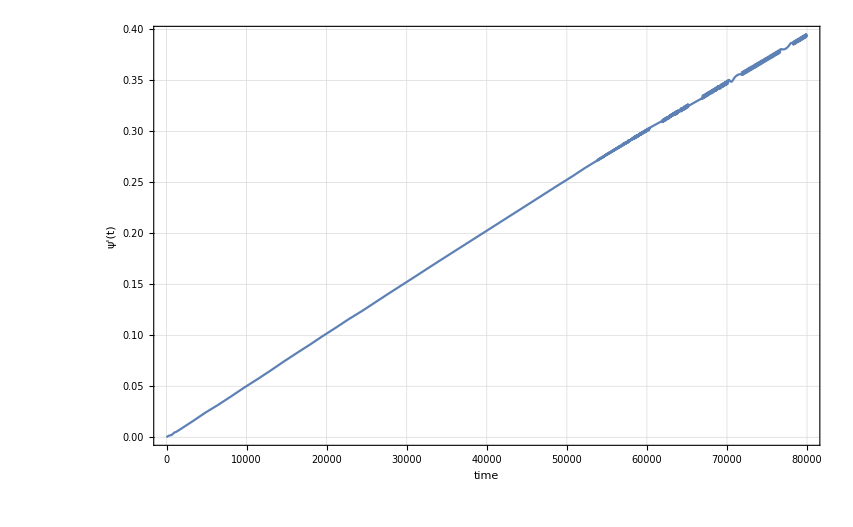

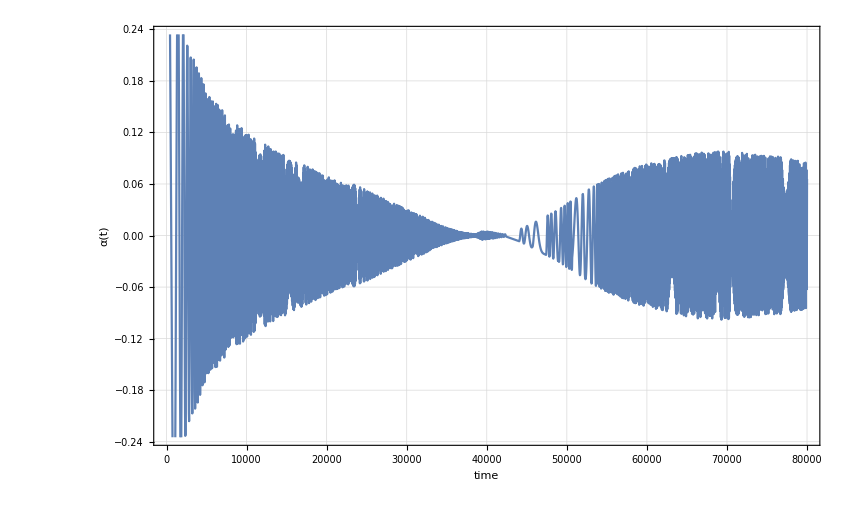

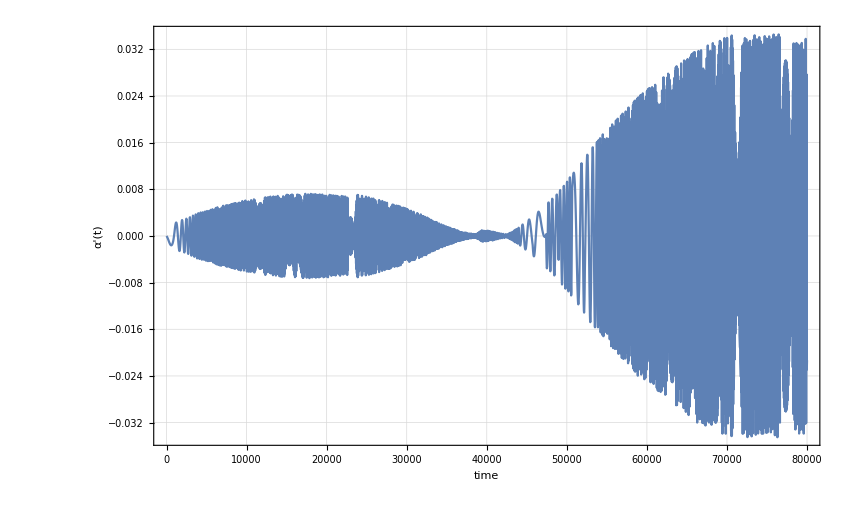

```mathematica
(*Data*)
μ=3.9877848 10^14;
Mp=1000;
l=50000;
rc=6870000;


dt = 0.01;
ranget = 80000;

alpha0 = Pi/6;
alphadsh0 = 0;
psi0 = 0;
psidsh0 = 0;

psiQ = 25000000;
alphaQ = 0;

(*Position vectors and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc Cos[θ[t]]}, {rc Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});
rp2[t]=rm[t]-({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp) (Transpose[rm'[t]].rm'[t]);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{(θ'[t]+ψ'[t]) Sin[α[t]]}, {-α'[t]}, {(θ'[t]+ψ'[t]) Cos[α[t]]}});

Subscript[ⅈ, 123]=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}});

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Subscript[U, p1]=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Subscript[U, p2]=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
V=Subscript[U, p1]+Subscript[U, p2];
θ[t]=√(μ/rc^3) t;
θ'[t]=√(μ/rc^3);
θ''[t]=0;

(*Lagrange equations*)
L=T-V;
eqn1=Simplify[D[D[L, ψ'[t]], t]-D[L, ψ[t]]-psiQ];
eqn2=Simplify[D[D[L, α'[t]], t]-D[L, α[t]]-alphaQ];
system=NDSolve[{eqn1==0,eqn2==0,α[0]==alpha0,α'[0]==alphadsh0,ψ[0]==psi0,ψ'[0]==psidsh0},{ψ,α},{t,0,80000},MaxSteps->∞,AccuracyGoal->Automatic,PrecisionGoal->Automatic,WorkingPrecision->10];
Plot[Evaluate[ψ[t]/.system],{t,0,80000},Frame->True,FrameTicks->Automatic,GridLines->Automatic,FrameLabel->{time,ψ[t]}]
Plot[Evaluate[ψ'[t]/.system],{t,0,80000},Frame->True,FrameTicks->Automatic,GridLines->Automatic,FrameLabel->{time,ψ'[t]}]
Plot[Evaluate[α[t]/.system],{t,0,80000},Frame->True,FrameTicks->Automatic,GridLines->Automatic,FrameLabel->{time,α[t]}]
Plot[Evaluate[α'[t]/.system],{t,0,80000},Frame->True,FrameTicks->Automatic,GridLines->Automatic,FrameLabel->{time,α'[t]}]
```

```mathematica
angle[t_]:=ψ[t]/.system[[1]];
angle2[t_]:=α[t]/.system[[1]];
thetas = Table[Evaluate[θ[t]],{t,0,ranget,dt}];
psis = Table[Evaluate[angle[t]],{t,0,ranget,dt}];
alphas = Table[Evaluate[angle2[t]],{t,0,ranget,dt}];
```

$Aborted

```mathematica
r = 35;
rp = 10;
earth={White, Sphere[{0,0,0},10]};
RC[t_] := {r*Cos[thetas[[t]]],r*Sin[thetas[[t]]],0};
RP1[t_]:= RC[t]+{rp*Cos[alphas[[t]]]*Cos[psis[[t]]+thetas[[t]]],rp*Cos[alphas[[t]]]Sin[psis[[t]]+thetas[[t]]],rp*Sin[alphas[[t]]]};
RP2[t_]:= RC[t]-{rp*Cos[alphas[[t]]]*Cos[psis[[t]]+thetas[[t]]],rp*Cos[alphas[[t]]]Sin[psis[[t]]+thetas[[t]]],rp*Sin[alphas[[t]]]};
P1[t_] := {Gray, Sphere[RP1[t],1]};
P2[t_] :={Gray, Sphere[RP2[t],1]};
tether1[t_]:={Black, Cylinder[{RC[t],RP2[t]},0.3]}
tether2[t_]:={White, Cylinder[{RC[t],RP1[t]},0.3]}
xaxis[t_] := {Red, Cylinder[{RC[t],1.5RC[t]},0.1]}
yaxis[t_] := {Green, Cylinder[{RC[t],RC[t]+0.5{-RC[t][[2]],RC[t][[1]],0}},0.1]}
zaxis[t_] := {Blue, Cylinder[{RC[t],RC[t]+0.5Norm[RC[t]]{0,0,1}},0.1]}
anim = Animate[Graphics3D[{earth,P1[t],P2[t],tether1[t],tether2[t],xaxis[t],yaxis[t],zaxis[t]},Boxed->True,PlotRange->50,ImageSize->Full],{t,1,ranget,1},AnimationRate->300,AnimationRunning->False, ContentSize->{600,600}]
```

```mathematica
RP11[t_]:= {rp*Cos[alphas[[t]]]*Cos[psis[[t]]],rp*Cos[alphas[[t]]]Sin[psis[[t]]],rp*Sin[alphas[[t]]]};
RP21[t_]:= -{rp*Cos[alphas[[t]]]*Cos[psis[[t]]],rp*Cos[alphas[[t]]]Sin[psis[[t]]],rp*Sin[alphas[[t]]]};
P11[t_] := {Gray, Sphere[RP11[t],1]};
P21[t_] :={Gray, Sphere[RP21[t],1]};
tether11[t_]:={Black, Cylinder[{{0,0,0},RP21[t]},0.3]}
tether21[t_]:={White, Cylinder[{{0,0,0},RP11[t]},0.3]}
xaxis2 := {Red, Thick, InfiniteLine[{{-12,0,0},{12,0,0}}]}
yaxis2 := {Black,Thick, InfiniteLine[{{0,-12,0},{0,12,0}}]}
zaxis2 := {Black, Thick,InfiniteLine[{{0,0,-12},{0,0,12}}]}

tracerange = 10000;
tracep1[t_]:={Red, Line[Table[RP11[x],{x,If[t-tracerange>0,t-tracerange,1],t,30}]]};
tracep2[t_]:={Blue, Line[Table[RP21[x],{x,If[t-tracerange>0,t-tracerange,1],t,30}]]};
Subscript[e, 2][t_]:={-Sin[psis[[t]]],Cos[psis[[t]]],0}
ralpha[t_]:= RotationTransform[-alphas[[t]],Subscript[e, 2][t]]
Subscript[e, 1][t_]:=RP11[t]
Subscript[e, 3][t_]:= Cross[Subscript[e, 1][t],Subscript[e, 2][t]]

oneax[t_]:= {Green,Thick, Line[{{0,0,0},20*Normalize[Subscript[e, 1][t]]}]}
twoax[t_]:= {Green,Thick, Line[{{0,0,0},20*Normalize[Subscript[e, 2][t]]}]}
threeax[t_]:= {Green,Thick, Line[{{0,0,0},20*Normalize[Subscript[e, 3][t]]}]}
alphaxy[t_] := {rp*Cos[alphas[[t]]]*Cos[psis[[t]]],rp*Cos[alphas[[t]]]Sin[psis[[t]]],0};
up[t_] := {Blue, Dashed,Line[{{alphaxy[t],RP11[t]}}]}
out[t_] := {Blue, Dashed, Line[{{alphaxy[t],{0,0,0}}}]}

flat = {Blue, Opacity[0.1],InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]};
anim2 = Animate[Graphics3D[{flat,P11[t],P21[t],xaxis2,yaxis2,zaxis2,tether11[t],tether21[t],up[t],out[t],oneax[t],twoax[t],threeax[t],tracep1[t],tracep2[t]},Boxed->False,PlotRange->20,ImageSize->Full],{t,1,ranget,1},AnimationRate->300,AnimationRunning->False, ContentSize->{800,800}]
```

```mathematica
tlength=250000;
rR=6870000;
image=Import[FileNameJoin[{NotebookDirectory[],"earth.jpg"}]];
earth3={Translate[First@SphericalPlot3D[6371000,{theta,0,Pi},{phi,0,2 Pi},Mesh->None,TextureCoordinateFunction->({#5,1-#4}&),PlotStyle->Directive[Texture[image]],Lighting->"Neutral",Axes->False,Boxed->False],{0,0,0}]};
RC3[t_] := {rR*Cos[thetas[[t]]],rR*Sin[thetas[[t]]],0};
RP13[t_]:= RC3[t]+{tlength*Cos[alphas[[t]]]*Cos[psis[[t]]+thetas[[t]]],tlength*Cos[alphas[[t]]]Sin[psis[[t]]+thetas[[t]]],tlength*Sin[alphas[[t]]]};
RP23[t_]:= RC3[t]-{tlength*Cos[alphas[[t]]]*Cos[psis[[t]]+thetas[[t]]],tlength*Cos[alphas[[t]]]Sin[psis[[t]]+thetas[[t]]],tlength*Sin[alphas[[t]]]};
P13[t_] := {Black,  Sphere[RP13[t],20000]};
P23[t_] :={Black, Sphere[RP23[t],20000]};
tether13[t_]:={Gray, Thick,Line[{RC3[t],RP23[t]}]}
tether23[t_]:={Gray, Thick, Line[{RC3[t],RP13[t]}]}
xaxis3[t_] := {Red,Thick, Line[{RC3[t],1.1RC3[t]}]}
yaxis3[t_] := {Green, Thick,Line[{RC3[t],RC3[t]+0.1{-RC3[t][[2]],RC3[t][[1]],0}}]}
zaxis3[t_] := {Blue, Thick,Line[{RC3[t],RC3[t]+0.1Norm[RC3[t]]{0,0,1}}]}
camerapoint[t_] :=RC3[t]+0.4{RC3[t][[1]],RC3[t][[2]]-4000000,3000000}
scene[t_]:=Graphics3D[{earth3,P13[t],P23[t],tether13[t],tether23[t],xaxis3[t],yaxis3[t],zaxis3[t]},Boxed->False,PlotRange->8000000,ImageSize->{1080,600},ViewVector->{camerapoint[t],RC3[t]},Lighting->{"Point", White,{0,0,0}}]
anim3 = Animate[scene[t],{t,1,ranget,1},AnimationRate->1000,AnimationRunning->False]
```

```mathematica
SetOptions[$FrontEnd,"DynamicUpdating"->True]
```